```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<FunctionRepo`
```

### argumentCount

```mathematica
?argumentCount
```

Find the highest numbered slot in a function:

```mathematica
argumentCount[Function[#^2]]
```

1

```mathematica
argumentCount[Function[#1 + #2]]
```

2

```mathematica
argumentCount[Function[{x,y,z},Sin[x + y/z]]]
```

3

In this function, slot 2 goes unused, but it will still be counted:

```mathematica
argumentCount[Function[#1 + #3]]
```

3

Slots in inner functions will not be counted:

```mathematica
argumentCount[
Function[
Function[#1+#2+#3][#1,2#1,3#1]
]
]
```

1

A function that uses SlotSequence will be counted as having infinite arguments:

```mathematica
argumentCount[Function[Plus[##]]]
```

∞

String slots will be counted as being part of the first argument:

```mathematica
argumentCount[Function[#a  + #b]]
```

1

```mathematica
argumentCount[Function[#a  + #b+#2]]
```

2

argumentCount works with compiled functions:

```mathematica
argumentCount[Compile[{x,y,z},Sqrt[x y z]]]
```

3

A function that uses SlotSequence will be counted as having infinite arguments:

```mathematica
argumentCount[Function[Plus[#1, #2,##]]]
```

∞

This behavior can be changed with the "IgnoreSlotSequence" option:

```mathematica
argumentCount[Function[Plus[#1,#2, ##]], "IgnoreSlotSequence"-> True]
```

2

### AsynchronousDynamicModule

```mathematica
AsynchronousDynamicModule@DynamicModule[{x},Dynamic[First[x]],SynchronousInitialization->False,Initialization:>(x={};
Pause[3];
AppendTo[x,1])]
```

```mathematica
AsynchronousDynamicModule@DynamicModule[{x},Dynamic[Print["Hi!"];
First[x]],SynchronousInitialization->False,Initialization:>(x={};
Pause[3];
AppendTo[x,1])]
```

```mathematica
AsynchronousDynamicModule[DynamicModule[{x},Dynamic[x],SynchronousInitialization->False,Initialization:>(x={};
Pause[1];
AppendTo[x,1];
Pause[1];
AppendTo[x,2];
Pause[1];
AppendTo[x,3];
Pause[1];
AppendTo[x,4];)],Dynamic@ProgressIndicator[Length[x],{0,4}]]
```

```mathematica
AsynchronousDynamicModule[DynamicModule[{x,start,updateAction},Dynamic[Column[{x,Slider[Dynamic[start],{0,10,1}],Button["Update",updateAction[start],Method->"Queued",ImageSize->All]}]],SynchronousInitialization->False,Initialization:>(start=0;
updateAction[startVal_]:=(initQ=False;
x={};
Pause[1];
AppendTo[x,startVal+1];
Pause[1];
AppendTo[x,startVal+2];
Pause[1];
AppendTo[x,startVal+3];
Pause[1];
AppendTo[x,startVal+4];
initQ=True);
updateAction[start])],Dynamic@ProgressIndicator[Length[x],{0,4}],initQ]
```

### conditionedMultinormalDistribution

```mathematica
?conditionedMultinormalDistribution
```

```mathematica
dist=MultinormalDistribution[{μ1,μ2},{{Σ11,Σ12},{Σ12,Σ22}}];
conditionedMultinormalDistribution[dist,2->x2]
```

```mathematica
conditionedMultinormalDistribution[dist,2->x2,1]
```

### convertDataFormat

```mathematica
?convertDataFormat
```

### CrossValidateModel

```mathematica
?CrossValidateModel
```

```mathematica
data = RandomVariate[PoissonDistribution[2],100];
Histogram[data,{1},PlotRange->All]
```

```mathematica
val=CrossValidateModel[data,PoissonDistribution[λ]];
val//TableForm
```

### deleteContainedStrings

```mathematica
?deleteContainedStrings
```

### ExpressionToFunction

```mathematica
?ExpressionToFunction
```

Create a function from a simple polynomial:

```mathematica
polyFun=ExpressionToFunction[1+2 x + x^2,x]
```

Evaluate the polynomial at a given value:

```mathematica
polyFun[1]
```

Convert a multivariate PDF to a function:

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
```

```mathematica
pdfFun=ExpressionToFunction[Evaluate[pdf],x,y]
```

```mathematica
N@pdfFun[0,1]
```

Bind x and y to the first slot of the function as a vector:

```mathematica
pdfFun2=ExpressionToFunction[Evaluate[pdf],{x,y}]
```

```mathematica
N@pdfFun2[{0,1}]
```

Bind arguments to keys in an Association:

```mathematica
powerFun=ExpressionToFunction[x^y,x->"Base",y-> "Exponent"]
```

```mathematica
powerFun[<|"Base"->2,"Exponent"->3|>]
```

Bind multiple symbols to a single slot:

```mathematica
ExpressionToFunction[x+y,{x,y}][{E, Pi}]
```

```mathematica
powerFun2=ExpressionToFunction[x^y,{x,y}->"BaseExponentTuple"]
```

```mathematica
powerFun2[<|"BaseExponentTuple"->{2,3}|>]
```

Combine names slots with positional slots:

```mathematica
powerFun3=ExpressionToFunction[z*x^y,z->"z",{x,y}->2]
```

```mathematica
powerFun3[<|"z"->Pi|>,{E,2}]
```

Use the Attributes option to return a function that holds its arguments:

```mathematica
addToSymbol=ExpressionToFunction[var=var+val,var,val,Attributes->HoldFirst]
```

```mathematica
counter=1
```

```mathematica
addToSymbol[counter,2]
```

```mathematica
counter
```

Group x and y together as a vector argument and map over a list of points:

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
```

```mathematica
pdfVectorFun=ExpressionToFunction[Evaluate[pdf],{x,y}]
```

```mathematica
dataRange = {{-3,3},{-3,3}};
```

```mathematica
points=Map[pdfVectorFun, CoordinateBoundsArray[dataRange,0.1],{2}];
```

```mathematica
ListContourPlot[points,DataRange->dataRange]
```

Add a parameter of the PDF as an argument:

```mathematica
parameterizedPDF=ExpressionToFunction[
Evaluate[
PDF[BinormalDistribution[ρ],{x,y}]
],
{x,y},
ρ
]
```

```mathematica
parameterizedPDF[{2,1},1/10]
```

Convert the solution of a differential equation to a function:

```mathematica
sol = DSolveValue[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]
```

```mathematica
dSolveFun=ExpressionToFunction[Evaluate[sol],x,a]
```

```mathematica
dSolveFun[10,1]
```

Represent the function at parameter value a=10 with Curry, then map over a range of x-values:

```mathematica
AssociationMap[
Curry[dSolveFun][10],
Range[0,10,0.1]
]//ListPlot
```

### firstMatchingValue

```mathematica
?firstMatchingValue
```

```mathematica
firstMatchingValue[{Print["before"],10,Print["after"]},_Integer]
```

```mathematica
x=2;
{x,
firstMatchingValue[{a,2,++x,1+3,5},_Integer?OddQ],
x}
```

### kullbackLeiblerDivergence

```mathematica
?kullbackLeiblerDivergence
```

```mathematica
kullbackLeiblerDivergence[BinormalDistribution[ρ1],BinormalDistribution[ρ2]]
```

```mathematica
kullbackLeiblerDivergence[
EmpiricalDistribution[{"a","b","b"}],
EmpiricalDistribution[{"a","b","c"}]
]
```

```mathematica
kullbackLeiblerDivergence[
BernoulliDistribution[p],
EmpiricalDistribution[{0,0,1}]
]
```

### maximumSpacingEstimation

```mathematica
?maximumSpacingEstimation
```

### MultiNonlinearModelFit

```mathematica
?MultiNonlinearModelFit
```

```mathematica
data=RandomVariate[BinormalDistribution[0.7],{2,100}];
data[[2,All,2]]+=2.;

model=MultiNonlinearModelFit[
data,
 {a x+ b1,a x + b2},{a,b1,b2},
{x}
]
```

```mathematica
Show[
ListPlot[data],
Plot[Evaluate[Table[Normal[model],{n,Length[data]}]],{x,-5,5}]
]
```

### SparseAssociation

```mathematica
SparseAssociation::usage
```

```mathematica
array=RandomInteger[2,{4,2,3}]
```

```mathematica
sparseAssoc=SparseAssociation[SparseArray[array,Automatic,1],{"a","b","c","d"},0]
```

```mathematica
sparseAssoc===SparseAssociation[Normal[sparseAssoc],Keys[sparseAssoc]]
```

```mathematica
Normal@Values@sparseAssoc===array
```

```mathematica
Length[sparseAssoc]
ArrayDepth[sparseAssoc]
Dimensions[sparseAssoc]
Keys[sparseAssoc]
```

```mathematica
sparseAssoc["a","b","c"]
%===array[[1,2,3]]
```

```mathematica
sparseAssoc[["a",All, {1, 3}]]===sparseAssoc[[1,All,{"a","c"}]]
```

```mathematica
sparseAssoc[["b",All,{"a","c"}]]
Normal@Values@%===array[[2,All,{1,3}]]
```

```mathematica
Map[#^2&,sparseAssoc,{3}]
Normal@Normal[%]
```

```mathematica
ArrayRules@sparseAssoc
```

```mathematica
SparseAssociation[RandomInteger[2,{3,3,3}],Partition[Take[Alphabet[],9],3]]
ArrayRules[%]
```

### SelfReferentialAssociation

```mathematica
?SelfReferentialAssociation
```

```mathematica
sAssoc=SelfReferentialAssociation[
<|
"a"-> 1.,
"b"-> TemplateExpression[Sin@TemplateSlot["a"]] ,
"c"-> StringTemplate["`a` + `b`"]
|>
]
```

SelfReferentialAssociation[…]

```mathematica
sAssoc["a"]
sAssoc["b"]
sAssoc["c"]
```

1.

0.841471

1.0 + 0.841471

```mathematica
Normal[sAssoc]
Keys[sAssoc]
Values[sAssoc]
Length[sAssoc]
```

<|a→1.,b→TemplateExpression[Sin[TemplateSlot[a]]],c→TemplateObject[{TemplateSlot[a], + ,TemplateSlot[b]},CombinerFunction→StringJoin,InsertionFunction→TextString]|>

{a,b,c}

{1.,0.841471,1.0 + 0.841471}

3

```mathematica
sAssoc[["b"]]
sAssoc[[{"b","c"}]]
sAssoc[[2]]
sAssoc[[{2,3}]]
```

0.841471

<|b→0.841471,c→1.0 + 0.841471|>

0.841471

<|b→0.841471,c→1.0 + 0.841471|>

```mathematica
Join[sAssoc,<|"a"->3.|>]
%//Values
Append[sAssoc,"a" -> 3.]
%//Values
Prepend[sAssoc,"a" -> 3.]
%//Values
```

SelfReferentialAssociation[…]

{3.,0.14112,3.0 + 0.14112}

SelfReferentialAssociation[…]

{0.14112,3.0 + 0.14112,3.}

SelfReferentialAssociation[…]

{3.,0.14112,3.0 + 0.14112}

### tukeyMedianPolish

```mathematica
?tukeyMedianPolish
```

```mathematica
matrix=N@RandomInteger[10,{4,6}];
Grid[matrix]
```

```mathematica
polish = tukeyMedianPolish[matrix];
Grid[polish,Dividers->{-2->True,-2->True}]
```

### multiSet

```mathematica
<<FunctionRepo`
```

```mathematica
?multiSet
```

```mathematica
Union[multiSet[{1,1,2}],multiSet[{2,2,1,3}]]//Normal
```

```mathematica
Intersection[multiSet[{1,1,2,3,3}],multiSet[{1,1,1,3}]]
```

```mathematica
Values@Complement[multiSet[{1,1,2}],multiSet[<|1->n,2->2,3->1|>]]
```

### checkboxLegended

```mathematica
<<FunctionRepo`
```

```mathematica
dataset=<|"Dataset1"-> Range[10],"Dataset2"-> Range[10,1,-1]|>;
checkboxLegended[
ListPlot[dataset]
]
```

### expressionToFunction

```mathematica
expressionToFunction::usage
```

```mathematica
polyFun=expressionToFunction[1+2 x + x^2,x]
polyFun[1]
```

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
pdfFun=expressionToFunction[Evaluate[pdf],x,y]
```

```mathematica
powerFun=expressionToFunction[x^y,x->"Base",y-> "Exponent"]
powerFun[<|"Base"->2,"Exponent"->3|>]
```

```mathematica
expressionToFunction[x+y,{x,y}][{E, Pi}]
```

```mathematica
powerFun2=expressionToFunction[x^y,{x,y}->"BaseExponentTuple"]
powerFun2[<|"BaseExponentTuple"->{2,3}|>]
```

```mathematica
pdf = PDF[BinormalDistribution[1/3],{x,y}]
pdfVectorFun=expressionToFunction[Evaluate[pdf],{x,y}]
dataRange = {{-3,3},{-3,3}};
points=Map[pdfVectorFun, CoordinateBoundsArray[dataRange,0.1],{2}];
ListContourPlot[points,DataRange->dataRange]
```

### conditionalProductDistribution

```mathematica
<<FunctionRepo`
```

```mathematica
conditionalProductDistribution::usage
```

```mathematica
conditionalProductDistribution[x\[Distributed]NormalDistribution[0,1]]
```

```mathematica
conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p]]
conditionalProductDistribution[k\[Distributed]BinomialDistribution[k,p]]
conditionalProductDistribution[p \[Distributed] BetaDistribution[α,β], k\[Distributed]BinomialDistribution[n,p]]
conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p], p \[Distributed] BetaDistribution[α,β]]
```

```mathematica
PDF[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{k,p}]
```

```mathematica
Likelihood[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{{k,p},{3,1/2}}]
LogLikelihood[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]],{{k,p},{3,1/2}}]
```

```mathematica
Graph@conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[α,β]]
Graph@conditionalProductDistribution[l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[n,p],p\[Distributed]BetaDistribution[α,β],n\[Distributed]GeometricDistribution[1/2]]
```

```mathematica
dist=conditionalProductDistribution[
l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[n,p],
p\[Distributed]BetaDistribution[α+1,β+1],{n,α,β}\[Distributed]ProductDistribution[{GeometricDistribution[1/2],3}]
]
Graph[dist]
rv1=RandomVariate[dist]
rv2=RandomVariate[dist,3]
LogLikelihood[dist,rv2]
Likelihood[dist,rv2]
Log[%]==%%
PDF[dist,rv2]
Times@@%==%%%
PDF[dist,rv1]
Likelihood[dist,{rv1}]
%==%%
```

```mathematica
dist=conditionalProductDistribution[
l\[Distributed]GeometricDistribution[p/(k+1)],k\[Distributed]BinomialDistribution[v1,p],
p\[Distributed]BetaDistribution[v2+1,v3+1],v\[Distributed]ProductDistribution[{GeometricDistribution[1/2],3}]
]
Graph[dist]
rv1=RandomVariate[dist]
rv2=RandomVariate[dist,3]
LogLikelihood[dist,rv2]
Likelihood[dist,rv2]
Log[%]==%%
PDF[dist,rv2]
Times@@%==%%%
PDF[dist,rv1]
Likelihood[dist,{rv1}]
%==%%
```

```mathematica
Graph@conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{σ1,σ2},ρ],ρ\[Distributed]BetaDistribution[1,2],{σ1,σ2}\[Distributed]MultinormalDistribution[{10,10},{{1,0},{0,1}}]]
```

```mathematica
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]]]
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]],3]
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[10,p],p \[Distributed] BetaDistribution[1,2]],{5,3}]
```

```mathematica
RandomVariate[conditionalProductDistribution[k\[Distributed]BinomialDistribution[n,p],p \[Distributed] BetaDistribution[1,2]]]
```

```mathematica
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]]]
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]],3]
RandomVariate[conditionalProductDistribution[{a,b}\[Distributed]BinormalDistribution[{μ1,μ2},{1,2},0.3],{μ1,μ2} \[Distributed] BinormalDistribution[0.5]],{5,3}]
```

```mathematica
RandomVariate[
conditionalProductDistribution[
x\[Distributed]MultinormalDistribution[μ,ν Σ],
ν\[Distributed]InverseGammaDistribution[5,10],
μ\[Distributed]MultinormalDistribution[{0,0},Σ],
Σ\[Distributed]InverseWishartMatrixDistribution[10,{{1,1/3},{1/3,1}}]
],
10
]
```

```mathematica
normalInverseWishartDistribution[μ0_,λ_,Ψ_,ν_]:= conditionalProductDistribution[
μ\[Distributed]MultinormalDistribution[μ0,Σ/λ],
Σ\[Distributed]InverseWishartMatrixDistribution[ν,Ψ]
];
```

```mathematica
RandomVariate[normalInverseWishartDistribution[{1,-3},5,({{1, 1/2}, {1/2, 2}}),7],5]
```

```mathematica
posterior[μ0_,λ_,Ψ_,ν_]:=conditionalProductDistribution[
X\[Distributed]MultinormalDistribution[μ,Σ],
{μ,Σ}\[Distributed]normalInverseWishartDistribution[μ0,λ,Ψ,ν]
]
```

```mathematica
RandomVariate[posterior[{1,-3},5,({{1, 1/2}, {1/2, 2}}),7],5]
```

### mergeByKey

```mathematica
<<FunctionRepo`
```

```mathematica
mergeByKey::usage
```

```mathematica
mergeByKey[{}, {}]
mergeByKey[{}, {a->1}]
mergeByKey[{}, {a->1},f]
mergeByKey[{}]@{}
mergeByKey[{a->1}]@{}
mergeByKey[{a->1},f]@{}
```

```mathematica
mergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare}]
mergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare,c-> foo}]
mergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{a->Total,b->RootMeanSquare},foo]
```

```mathematica
mergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{Key[a]->Total,b->RootMeanSquare}]
mergeByKey[{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>},{Key[a]->Total,b->RootMeanSquare},foo]
```

```mathematica
mergeByKey[{a->Total,b->RootMeanSquare}]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
mergeByKey[{a->Total,b->RootMeanSquare,c-> foo}]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
mergeByKey[{a->Total,b->RootMeanSquare},foo]@{<|a->1,b->2|>,<|c-> Pi|>,<|a->5,b->10|>}
```

```mathematica
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{{a,b}-> Total, c-> Mean}]
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{{a,b}-> Total},Mean]
MergeByKey[{<|a->1,b->2|>,<|a->5,b->10,c-> Pi|>,<|c->E|>},{c-> Mean},Total]
```

```mathematica
mergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{{a}-> Total}]
mergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{Key[{a}]-> Total}]
mergeByKey[{<|{a}->1,b->2|>,<|{a}->5,b->10|>},{{Key[{a}],b}-> Total}]
```

### graphicsToGraph

```mathematica
?graphicsToGraph
```

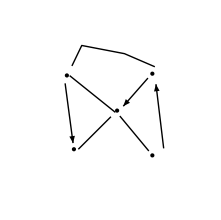
```mathematica
graph=graphicsToGraph[
-Graphics-
]
```

### GroupCases

```mathematica
<<FunctionRepo`
```

```mathematica
?GroupCases
```

```mathematica
GroupCases[{1,2,3.,x},_Integer]
```

```mathematica
GroupCases[{1,2,3.,x},i_Integer:>i/2]
```

```mathematica
GroupCases[{1,2,3.,x,4},i_Integer:>With[{j=i/2},j/;EvenQ[j]]]
```

```mathematica
GroupCases[{1,2,3.,x},{_Integer,_Real}]
```

```mathematica
GroupCases[{1,2,3.,x},<|"Int"-> _Integer,"Float"-> _Real,"NAN"-> _|>]
```

```mathematica
GroupCases[{1,2,3.,x},{_Integer,_Real,_Complex}]
```

```mathematica
test=RandomChoice[{1,1.},10^3];
GroupBy[test,IntegerQ];//RepeatedTiming
GroupCases[test,_Integer];//RepeatedTiming
```

### ScalableContentWindow

```mathematica
?ScalableContentWindow
```

```mathematica
<<FunctionRepo`
```

```mathematica
ScalableContentWindow[Graphics[Disk[]]]
```

```mathematica
ScalableContentWindow[
Block[{x},
Plot[Evaluate@Table[Labeled[x^n,x^n],{n,1,3}],{x,-3,3},PlotLabel->"Polynomials"]
]
]
```

```mathematica
ScalableContentWindow[
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{{a,1},ControlType->InputField}]
]
```

### SymbolicSort

```mathematica
?SymbolicSort
```

```mathematica
<<FunctionRepo`
```

```mathematica
SymbolicSort[{Exp[x],x},x]
```

```mathematica
SymbolicSort[{x,Log[x],Exp[x],x^2+1},x,x>0]
SymbolicSort[{x,Log[x],Exp[x],x^2+1},x,x>0,Reals,Graph]
```

```mathematica
SymbolicSort[{x,√(x^2)},x,x>0]
SymbolicSort[{√(x^2),x},x,x>0]
```

```mathematica
SymbolicSort[{Exp[y],Exp[x],Exp[z]},{x,y,z},x<y<z]
SymbolicSort[{Exp[y],Exp[x],Exp[z]},{x,y,z},x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{y,Log[x],Exp[z]},{x,y,z},0<x<y<z]
SymbolicSort[{y,Log[x],Exp[z]},{x,y,z},0<x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{Exp[y],x,Exp[z],a},{x,y,z,a},0<x<y<z]
SymbolicSort[{Exp[y],x,Exp[z],a},{x,y,z,a},0<x<y<z,Reals,Graph]
```

```mathematica
SymbolicSort[{x,Log[x],Exp[x],x^2+1,Sin[x]},x,x>0,Reals,Graph]
```

### WithCachedValues

```mathematica
?WithCachedValues
```

```mathematica
<<FunctionRepo`
```

```mathematica
ClearAll[f]
f[x_]/;EvenQ[x] :=(Pause[1];Print[{x}];Cos[x]);
f[x_] :=(Pause[1];Print[x];Sin[x]);
f[args___] :=(Pause[1];Print[{args}];Sin[{args}]);
```

```mathematica
WithCachedValues[{f,g},{f[1],f[1],f[2],f[1],f[2],f[1],f[2],f[1,2],f[1,2]}]//AbsoluteTiming
```

```mathematica
DownValues[f]//TableForm
```